# TraCOV: What’s your risk level for COVID-19?

Jessica Shi, Claire Morton, Anwesha Das, Aranyo Ray

https://www.tracov.tech

Figure out which interval (in tens) the age input is in

```mathematica
findinterval[age_]:=First@Select[Map[Interval[#]&,Partition[{1,9,10,19,20,29,30,39,40,49,50,59,60,69,70,79,80,89,90,99},2]],IntervalMemberQ[#,age]&]
```

Select the data with the same sex and in the age interval

```mathematica
finddata2[sex_,age_]:=Select[(Select[ResourceData["Patient Medical Data for Novel Coronavirus COVID-19"][Select[!MissingQ[#Age]&&!MissingQ[#Sex]&]],IntervalMemberQ[findinterval[age],#Age]&]),ContainsAll[#,{sex}]&]
```

Find the population with the same demographic (data from the United Nations)

```mathematica
finddemo[sex_,age_]:=If[MatchQ[sex,Entity["Gender","Female"]],Which[Between[age,{0,9}],650021,Between[age,{10,19}],605324,Between[age,{20,29}],577734,Between[age,{30,39}],564666,Between[age,{40,49}],482532, Between[age,{50,59}],418797,Between[age,{60,69}],305665,Between[age,{70,79}],170518,Between[age,{80,89}],74710,Between[age,{90,99}],14408]
,Which[Between[age,{0,9}],692361,Between[age,{10,19}],648139,Between[age,{20,29}],650139,Between[age,{30,39}],652139,Between[age,{40,49}],482532, Between[age,{50,59}],414825,Between[age,{60,69}],286119,Between[age,{70,79}],141941,Between[age,{80,89}],49406,Between[age,{90,99}],6406]]
```

Calculate the risk level according to sex and age

```mathematica
calcrisk[sex_,age_]:=N[Length@finddata2[sex,age]/finddemo[sex,age]]*100
```

Find the confirmed case data for the country

```mathematica
countrydata[country_]:=
(First@Normal[Select[ResourceData["Epidemic Data for Novel Coronavirus COVID-19","WorldCountries"],MemberQ[#,country]&]])["ConfirmedCases"]
```

Plot the confirmed cases in the country

```mathematica
ccplot[country_]:=DateListPlot[countrydata[country]]
```

Find the increase in cases in the past five days

```mathematica
calccountryinc[country_]:=countrydata[country]["Values"][[-1]]-countrydata[country]["Values"][[-5]]
```

Find the ratio of case increase to the country’s population

```mathematica
calccountryrisk[country_]:=N[calccountryinc[country]/(QuantityMagnitude[CountryData[country, "Population"]])]*1000
```

Add the two risks to find total risk

```mathematica
calctotalrisk[country_, sex_, age_]:= N[calccountryrisk[country]+calcrisk[sex,age]]
```

Plot all the cases

```mathematica
plotcases[sex_, age_] :=GeoListPlot[Map[#["GeoPosition"]&, finddata2[sex, age]]//Normal]
```

Find the number of deaths out of confirmed cases in the gender/age group

```mathematica
calcdeathrate[sex_,age_] :=StringJoin[{ToString@ Length@Select[finddata2[sex,age],#["DeathQ"]&]," out of ",ToString@Length[finddata2[sex,age]]}]
```

Classify the risk into a “risk level”

```mathematica
riskgen[word_, color_] := Style[word, Background -> color]
```

```mathematica
risklevel[risk_] := Which[0≤ risk<.20,riskgen["Low Risk",LightGreen],.20≤ risk<.40,riskgen["Moderate Risk",LightYellow],.40≤ risk<.60,riskgen["High Risk",LightOrange],.60≤ risk<1,riskgen["Very High Risk",LightRed]]
```

Make a list of diseases/chronic conditions the user can choose from

```mathematica
diseases=Prepend[Normal@DeleteDuplicates@Flatten@DeleteMissing@ResourceData["Patient Medical Data for Novel Coronavirus COVID-19"][All,"ChronicDiseases"],"NONE"]
```

{NONE,diabetes,cerebral infarction,hypertension,colon cancer,Parkinson's disease,encephalomalacia,hip replacement,chronic bronchitis,stenocardia,coronary stent,hemorrhage of digestive tract,chronic obstructive pulmonary disease,chronic renal insufficiency,coronary heart disease,tuberculosis,frequent ventricular premature beat,hypertriglyceridemia,type 2 diabetes,lung cancer,asthma,prostate hypertrophy,hepatitis B,coronary bypass surgery,kidney disease,on dialysis,chronic kidney disease,valvular heart disease,diabetes mellitus,obesity,HIV positive,chronic pulmonary condition,myeloma,upper gastrointestinal bleeding,prerenal azotemia,cardiomyopathy,benign prostatic hyperplasia,bronchial asthma,impaired fasting glucose,dyslipidemia,atherosclerosis,atrial fibrillation,cerebrovascular infarct,cardiac disease,hypothyroidism,cardiovascular disease,prostate cancer,tongue cancer,benign prostatic hypertrophy,cardiac dysrhythmia,hyperthyroidism,myocarditis,cerebrovascular accident infarct,systemic arterial hypertension}

Find how many cases of the chronic condition were reported

```mathematica
finddisease[disease_]:=If [StringMatchQ[disease,"NONE"],"",StringJoin[{ToString@(First@Normal@Select[Tally@DeleteMissing@Flatten@ResourceData["Patient Medical Data for Novel Coronavirus COVID-19"][All,"ChronicDiseases"],MemberQ[#,disease]&])[[2]]," case(s)of " , disease," reported globally" }]]
```

Give a summary of all information

```mathematica
summary[country_,gender_,age_,disease_]:=Grid[{{"Your risk level is:", risklevel[calctotalrisk[country, gender, age]]}, {"Your risk is:", NumberForm[calctotalrisk[country, gender, age],3]}, {"Risk due to your country is:", NumberForm[calccountryrisk[country],3]}, {"Risk due to your age range and gender is:",NumberForm[ calcrisk[gender, age],3]},{ "Map of global cases of your age range and gender:", plotcases[gender, age]}, {"Plot of confirmed cases in your country:",ccplot[country]},{"Current death rate for cases of your age range and gender:", calcdeathrate[gender, age]},{Column[Map[finddisease[#]&,disease]]}}]
```

Example output

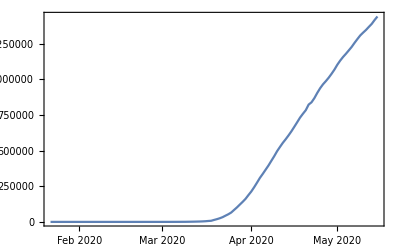
Your risk level is: | Very High Risk
Your risk is: | 0.621
Risk due to your country is: | 0.292
Risk due to your age range and gender is: | 0.33
Map of global cases of your age range and gender: | -Graphics-
Plot of confirmed cases in your country: | -Graphics-
Current death rate for cases of your age range and gender: | 14 out of 562
100 case(s)of hypertension reported globally
1 case(s)of hip replacement reported globally |

```mathematica
summary[LinguisticAssistant,LinguisticAssistant,72,{"hypertension","hip replacement"}]
```

Make a form page and send it to the cloud

```mathematica
CloudDeploy[ FormPage[{"gender" -> {Entity["Gender","Female"], Entity["Gender","Male"]}, "age" ->"Number", "country" -> "Country","ChronicConditions"->AnySubset[diseases]}, Grid[{{"Your risk level is:", risklevel[calctotalrisk[#country, #gender, #age]]}, {"Your risk is:", NumberForm[calctotalrisk[#country, #gender, #age],3]}, {"Risk due to your country is:", NumberForm[calccountryrisk[#country],3]}, {"Risk due to your age range and gender is:",NumberForm[ calcrisk[#gender, #age],3]},{ "Map of global cases of your age range and gender:", plotcases[#gender, #age]}, {"Plot of confirmed cases in your country:",ccplot[#country]},{"Current death rate for cases of your age range and gender:", calcdeathrate[#gender, #age]},{Column[Map[finddisease[#]&,#ChronicConditions]]}}] &, AppearanceRules -><|"Title" ->-Graphics- ,"Description"->"Please enter your gender, age, country, and any chronic conditions (you may select NONE or multiple) to find your estimated level of risk for contracting COVID-19. Chronic conditions may increase your vulnerability to COVID-19, but were not included in calculations. For the purposes of our informational tool, risk is defined as the proportion of people in our dataset of those infected who shared one or more of the characteristics of the user out of all people who share these characteristics. Risk does not represent a probability that the user will contract the coronavirus -- it is an informational number that we use to calculate the user's level of vulnerability based on his or her characteristics. Please comply with guidelines provided by your local and federal government."|> ,PageTheme-> "Red"],Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/5825a1fe-2878-4fcc-8792-99b693b026f7]